## Initialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,Axes->False};
```

```mathematica
density1={Evaluate@font,ColorFunction->"SunsetColors"};
density2={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->310};
density3={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->410};
export1={"AllowRasterization"->True,ImageResolution->800};
plot1={Frame->True,Evaluate@font,Axes->False};
plot2={Frame->True,PerformanceGoal->"Quality",ImageSize->310,Evaluate@font,Axes->False,PlotStyle->Thickness[0.004]};
```

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-5/2-λ/4 | -χ/(2 √5) | -λ/(√10) | 0 | 0 | 0
-χ/(2 √5) | 1/20 (-30-13 λ-4 χ^2) | -(3 √2 χ)/5 | -(3 λ)/(5 √2) | 0 | 0
-λ/(√10) | -(3 √2 χ)/5 | 1/20 (-17 λ-2 (5+8 χ^2)) | -(3 χ)/2 | -(3 λ)/(5 √2) | 0
0 | -(3 λ)/(5 √2) | -(3 χ)/2 | 1/20 (10-17 λ-36 χ^2) | -(7 √2 χ)/5 | -λ/(√10)
0 | 0 | -(3 λ)/(5 √2) | -(7 √2 χ)/5 | 1/20 (30-13 λ-64 χ^2) | -(9 χ)/(2 √5)
0 | 0 | 0 | -λ/(√10) | -(9 χ)/(2 √5) | 5/2-λ/4-5 χ^2)

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Energies

## Plotting spectrum

```mathematica
energies1=Eigenvalues[H[-1.5,χ]];
energies2=Eigenvalues[H[λ,0.845]];
```

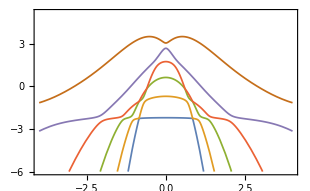
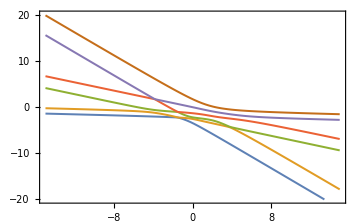

```mathematica
plotOpt={PlotPoints->80,Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->{Thickness[0.004]}};
{plA,plB}={Plot[energies1,{χ,-4,4},PlotRange->{Automatic,{-6,5.2}},Evaluate@plot2,FrameLabel->MaTeX/@{"\\chi","E /Ry"}],
Plot[energies2,{λ,-15,15},PlotRange->{Automatic,{-20,20}},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","E /Ry"}]}
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=10_energiesl.pdf",plA,"AllowRasterization"->True,ImageSize->330,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=10_energies2.pdf",plB,"AllowRasterization"->True,ImageSize->320,ImageResolution->800];
```

```mathematica
eigensys[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First]
]
eigensys1[λ_?NumericQ,χ_?NumericQ]:=
Sort@Eigenvalues[HC[λ,χ],Method->{"Banded"}
]
```

```mathematica
Plot3D[Query[1]@ND[eigensys1[λ,x],{x,2},χ]+Query[1]@ND[eigensys1[l,χ],{l,2},λ],{λ,-3,10},{χ,-1,1},ColorFunction->"SunsetColors",PlotPoints=10,ExclusionsStyle->{None, Red},Exclusions->Automatic,ClippingStyle->None,PerformanceGoal->"Quality"]
```

```mathematica
Plot[1-χ^2/(2j)(m+2j)-χ^2 j/2/.{j->4,m->4},{χ,-2,2}]
```

## Degeneracy

### Background

```mathematica
Sp[λ_,χ_]:=Sort[Eigenvalues[H[λ,χ]]];
dSp[λ_,χ_]:=Abs[Sp[λ,χ]⟦1;;dim-1⟧-Sp[λ,χ][[2;;dim]]];
```

```mathematica
difEn=DensityPlot[dSp[λ,χ]⟦#⟧,{λ,-5,5},{χ,-3,3},PlotPoints->30,PlotLegends->Automatic,Evaluate@densityPlotOptions,ScalingFunctions->"Log"]&/@Range[dim-1];
```

### Singularities

```mathematica
SpMin=ParallelTable[FindMinimum[{dSp[λ,χ][[#]],χ>-0.01,χ<1.5,λ<2,λ>-4},{{λ,l},{χ,x}},AccuracyGoal->30,PrecisionGoal->30,WorkingPrecision->30],{l,-4,2,0.2},{x,-0.2,1.7,0.2}]&/@Range[dim-1];
```

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 510 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {MaTeX`Private`λ,MaTeX`Private`χ} = {-1.86775,0.639911}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

FindMinimum::acceptlev: Solved to acceptable level.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::precw: The precision of the argument function ({{MaTeX`Private`λ>-4,MaTeX`Private`χ>-0.01,MaTeX`Private`λ<2,MaTeX`Private`χ<1.5}}) is less than WorkingPrecision (30.).

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::precw will be suppressed during this calculation.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

General::stop: Further output of FindMinimum::acceptlev will be suppressed during this calculation.

```mathematica
SpMinR[i_]:=Select[Flatten[SpMin[[i]],1],#[[1]]<10^-8&]
```

```mathematica
SpMinR[1]
```

{{0.,{λ→-0.500000001469129373710131858388,χ→0.77459665096454721755492300872}},{0.,{λ→-0.50000006035019106676031697134,χ→0.774596666000376354865863959276}}}

### Plot

```mathematica
lpl[i_]:=ListPlot[{λ,χ}/.SpMinR[i][[#,2]]&/@Range[Dimensions[SpMinR[i]][[1]]],PlotStyle->{Green,PointSize->0.015}]
layer[i_]:=Show[difEn[[i]],lpl[i]]
```

```mathematica
{layer[1],layer[2],layer[3]}
```

#### N = 7

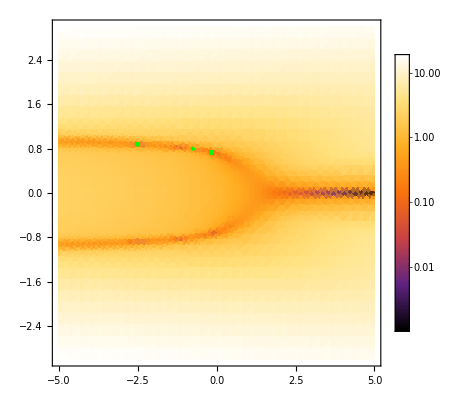
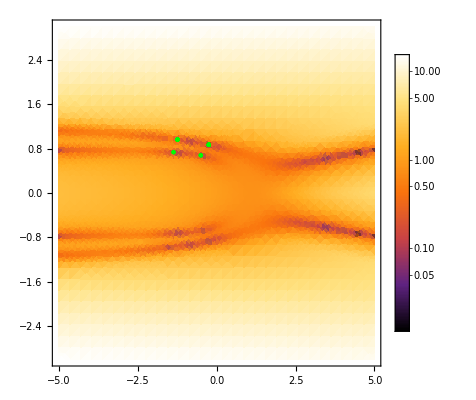
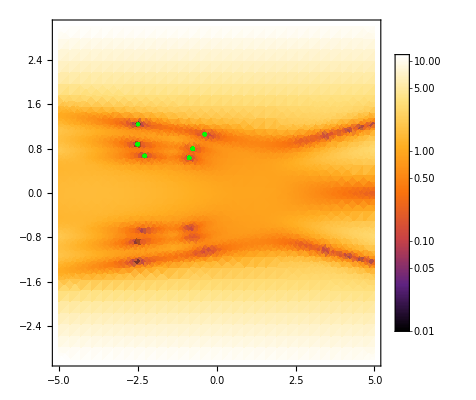
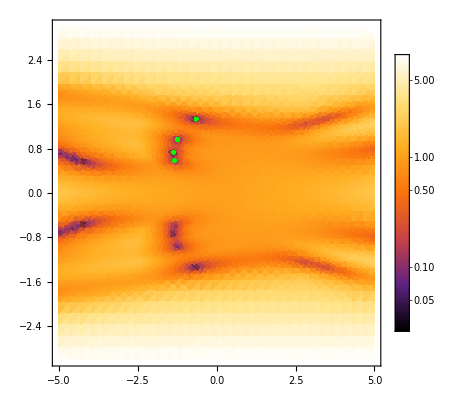
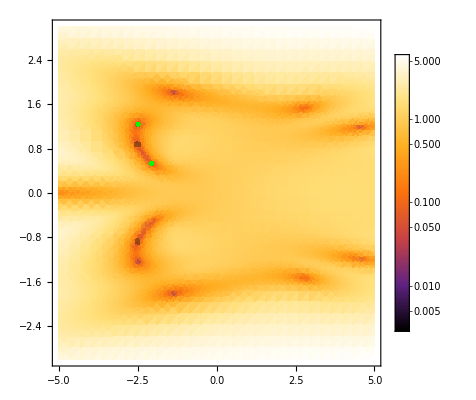
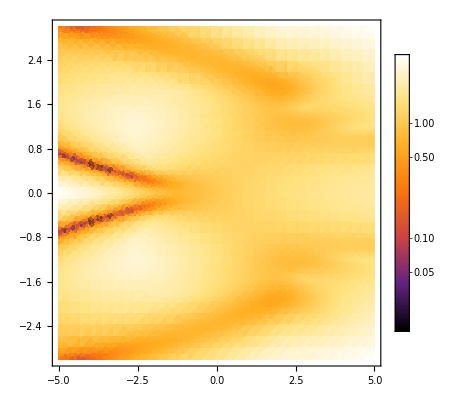
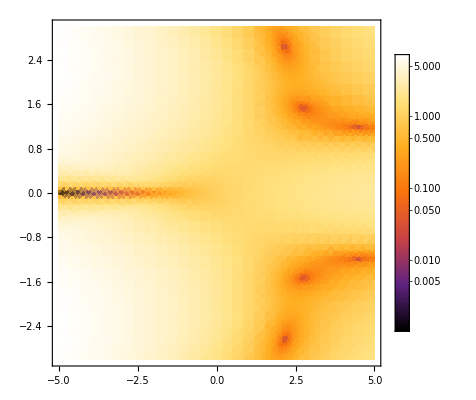

#### N = 6

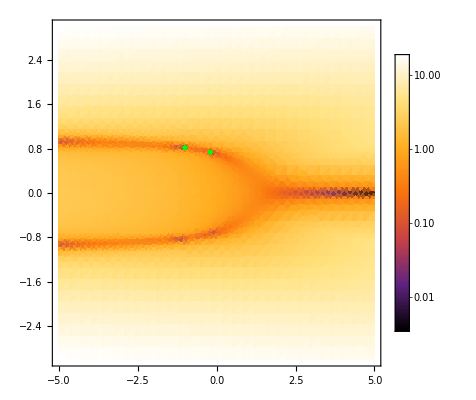
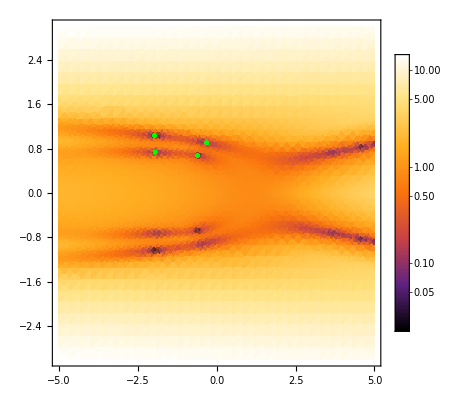
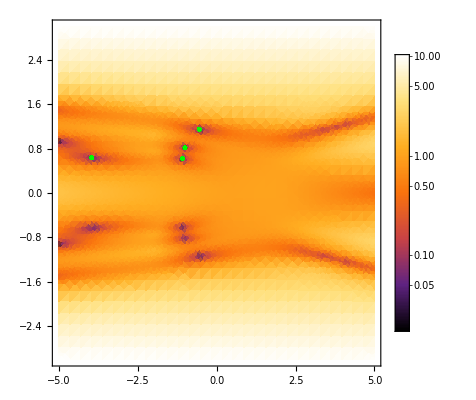
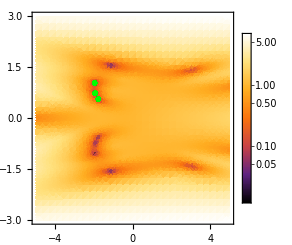
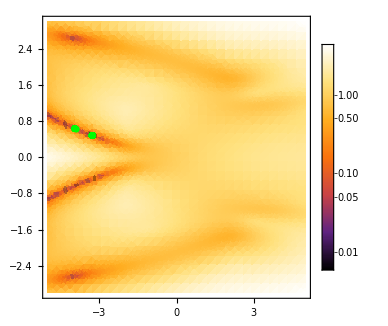
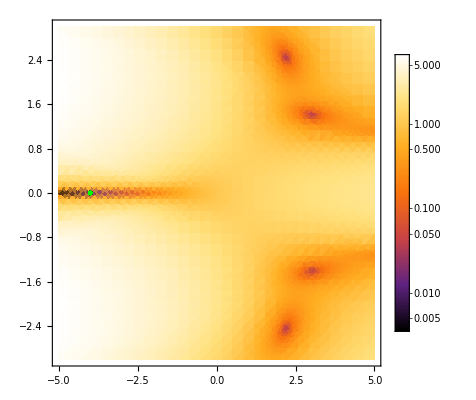

#### N = 5

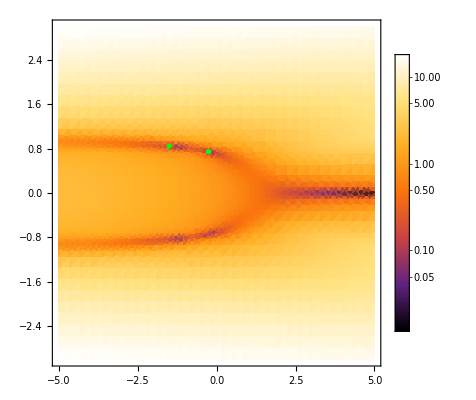
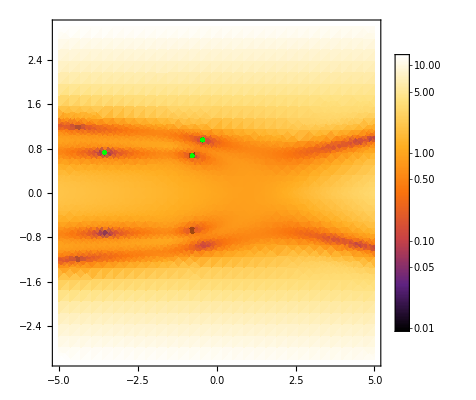
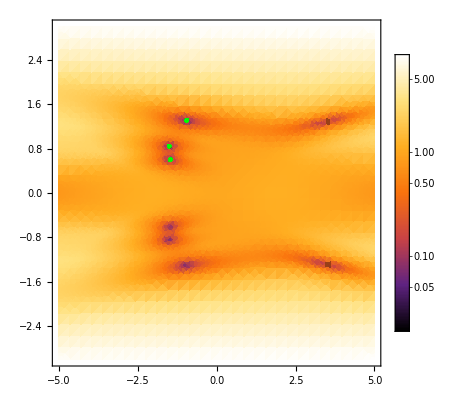
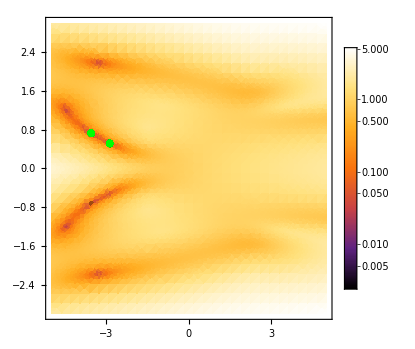
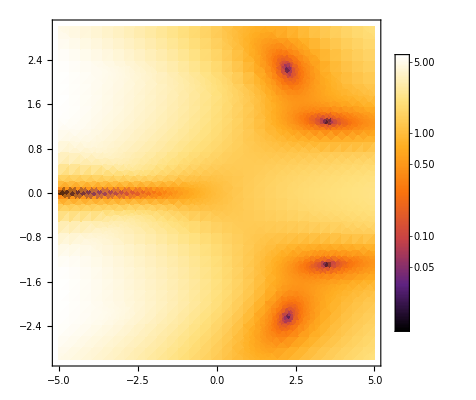

#### N = 4

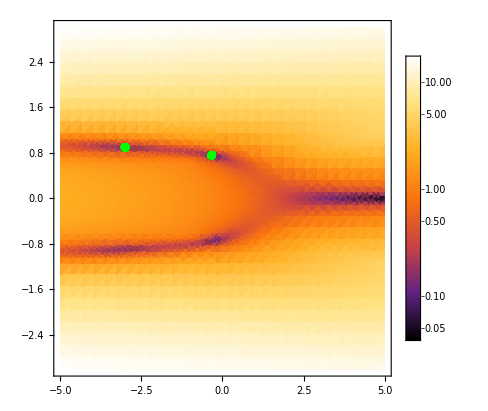
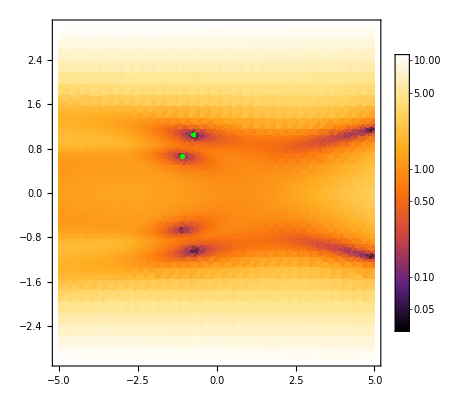
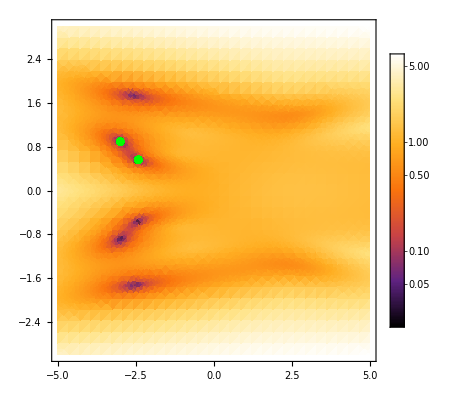
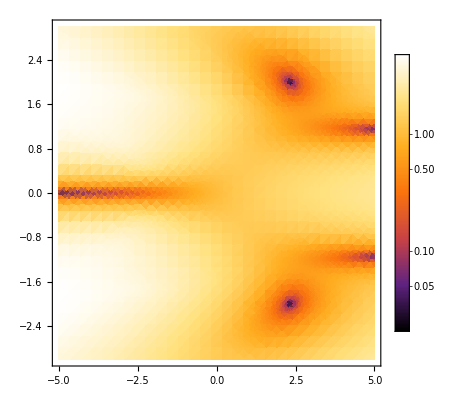

#### N = 3

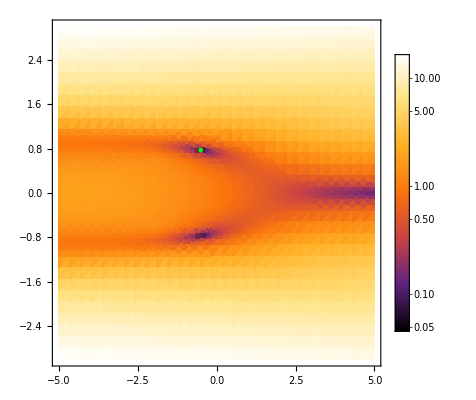
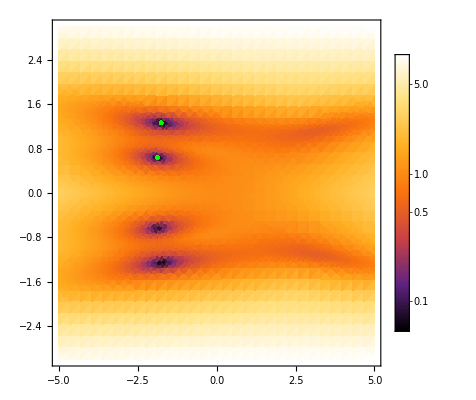
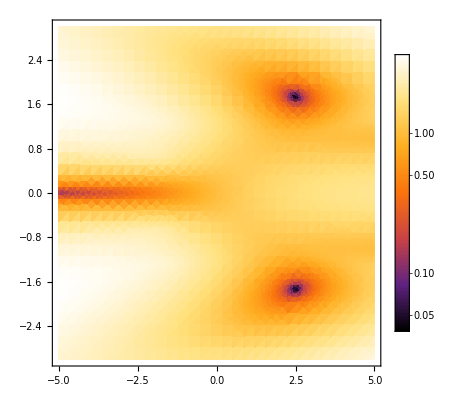

New images of the eigenvalues difference are added from the middle, the characteristics of the first and last images are not N - dependent.

## Singularity dependence on dimension

```mathematica
SpMinArray={};
```

```mathematica
For[nn=3,nn<25,nn++, 
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
Sp[λ_,χ_]:=Sort[Eigenvalues[H[λ,χ]]];
dSp[λ_,χ_]:=Abs[Sp[λ,χ]⟦1;;dim-1⟧-Sp[λ,χ][[2;;dim]]];

min=NMinimize[{dSp[λ,χ][[1]],χ>0.0001,χ<1,λ<1.4,λ>-10,χ^2<(λ-1)/(λ-2)+0.1},{λ,χ},AccuracyGoal->20,PrecisionGoal->20];
AppendTo[SpMinArray,{nn,min}]
]
```

```mathematica
SpMinArray
```

{{3,{0.,{λ→-0.5,χ→0.774597}}},{4,{0.,{λ→-3.,χ→0.894427}}},{5,{0.,{λ→-1.5,χ→0.845154}}},{6,{0.,{λ→-1.,χ→0.816497}}},{7,{0.,{λ→-0.750005,χ→0.797724}}},{8,{0.,{λ→-1.66666,χ→0.852803}}},{9,{7.66396×10^-10,{λ→-3.49996,χ→0.904533}}},{10,{0.,{λ→-2.33339,χ→0.87706}}},{11,{0.,{λ→-1.7499,χ→0.856345}}},{12,{0.,{λ→-1.39967,χ→0.840151}}},{13,{0.,{λ→-2.2503,χ→0.874484}}},{14,{0.,{λ→-3.66765,χ→0.907501}}},{15,{0.,{λ→-2.75956,χ→0.888763}}}}

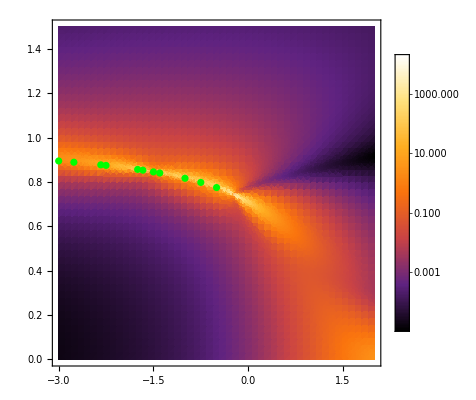

```mathematica
SpMinPlot=ListPlot[{λ,χ}/.SpMinArray[[#,2,2]]&/@Range[13],PlotStyle->Green];
Show[{det,SpMinPlot}]
```

```mathematica
cd={λ,χ}/.SpMinArray[[#,2,2]]&/@Range[13]
divPosition=ListPlot[Table[Callout[cd[[i-2]],i],{i,3,15}],Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ImageSize->Medium];
regr=Plot[√((1-l)/(2-l)),{l,-4,0},PlotStyle->{Gray,Thickness[0.004]}];
divPos=Show[{divPosition,regr}]
```

{{-0.5,0.774597},{-3.,0.894427},{-1.5,0.845154},{-1.,0.816497},{-0.750005,0.797724},{-1.66666,0.852803},{-3.49996,0.904533},{-2.33339,0.87706},{-1.7499,0.856345},{-1.39967,0.840151},{-2.2503,0.874484},{-3.66765,0.907501},{-2.75956,0.888763}}

-Graphics-

## E0 to E1

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
Sp01[λ_,χ_]:=Sort[Eigenvalues[H[λ,χ]]];
dSp01[λ_,χ_]:=Abs[Sp01[λ,χ]⟦1;;dim-1⟧-Sp01[λ,χ][[2;;dim]]];

min=NMinimize[{dSp01[λ,χ][[1]],χ>0.0001,χ<1,λ<1.4,λ>-10,χ^2<(λ-1)/(λ-2)+0.1},{λ,χ},AccuracyGoal->20,PrecisionGoal->20];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
eig2[λ_,χ_]:=Sort@Eigenvalues[H[λ,χ]];
diff[λ_,χ_]:=eig2[λ,χ][[2]]-eig2[λ,χ][[1]];
```

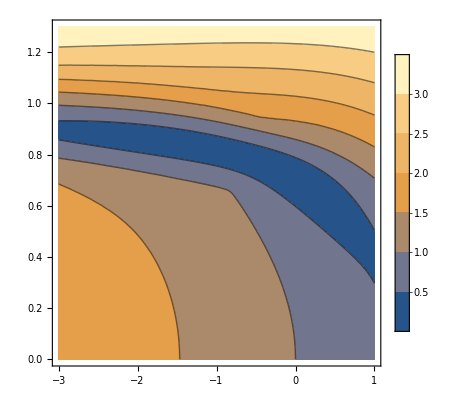

```mathematica
ContourPlot[diff[λ,χ],{λ,-3,1},{χ,0,1.3},PlotLegends->Automatic]
```

```mathematica
min=ParallelTable[FindMinimum[{diff[λ,χ],χ>0.0001,χ<1,λ<1.4,λ>-10,χ^2<(λ-1)/(λ-2)+0.1},{{λ,l},{χ,x}},AccuracyGoal->15,PrecisionGoal->15],{l,-2,1,0.2},{x,0,1.3,0.2}]
```

{{{0.000013455,{λ→-0.500022,χ→0.774597}},{0.0000288111,{λ→-0.499951,χ→0.774596}},{7.24595×10^-6,{λ→-0.500002,χ→0.774595}},{0.0000243411,{λ→-0.500043,χ→0.774604}},{0.0000128515,{λ→-0.500001,χ→0.774594}},{8.77548×10^-6,{λ→-0.500018,χ→0.774598}},{8.77548×10^-6,{λ→-0.500018,χ→0.774598}}},{{9.22268×10^-6,{λ→-0.499981,χ→0.774595}},{2.63363×10^-6,{λ→-0.500005,χ→0.774597}},{4.43009×10^-6,{λ→-0.500005,χ→0.774598}},{2.02776×10^-6,{λ→-0.499998,χ→0.774597}},{0.000173036,{λ→-0.499854,χ→0.774546}},{0.000224651,{λ→-0.49998,χ→0.774648}},{0.000224651,{λ→-0.49998,χ→0.774648}}},{{9.27222×10^-6,{λ→-0.499996,χ→0.774598}},{0.0000185699,{λ→-0.500035,χ→0.774598}},{0.0000271894,{λ→-0.499964,χ→0.774589}},{0.0000122863,{λ→-0.500013,χ→0.774595}},{0.0000306322,{λ→-0.500003,χ→0.77459}},{7.64034×10^-6,{λ→-0.500014,χ→0.774599}},{7.64034×10^-6,{λ→-0.500014,χ→0.774599}}},{{0.0000765772,{λ→-0.499949,χ→0.774575}},{0.0000291076,{λ→-0.499987,χ→0.774602}},{0.0000292189,{λ→-0.499941,χ→0.77459}},{0.0000105765,{λ→-0.500007,χ→0.774595}},{0.000056956,{λ→-0.500049,χ→0.774613}},{0.0000433723,{λ→-0.500054,χ→0.77461}},{0.0000433723,{λ→-0.500054,χ→0.77461}}},{{0.00001803,{λ→-0.499982,χ→0.774599}},{0.000384261,{λ→-0.500188,χ→0.774702}},{0.0000220024,{λ→-0.500011,χ→0.774603}},{2.63749×10^-6,{λ→-0.500005,χ→0.774597}},{0.0000185838,{λ→-0.499966,χ→0.774596}},{0.0000295158,{λ→-0.500037,χ→0.774606}},{0.0000295158,{λ→-0.500037,χ→0.774606}}},{{6.37071×10^-6,{λ→-0.499993,χ→0.774595}},{6.06004×10^-6,{λ→-0.500008,χ→0.774598}},{0.000102272,{λ→-0.499917,χ→0.774567}},{0.0000248084,{λ→-0.500032,χ→0.774604}},{0.000279444,{λ→-0.499967,χ→0.774527}},{9.6135×10^-6,{λ→-0.50001,χ→0.7746}},{9.6135×10^-6,{λ→-0.50001,χ→0.7746}}},{{0.0000329393,{λ→-0.500007,χ→0.774605}},{0.0036937,{λ→-0.503528,χ→0.775687}},{0.0000150253,{λ→-0.500011,χ→0.774594}},{0.0283486,{λ→-0.480905,χ→0.766443}},{0.0000124495,{λ→-0.499997,χ→0.774593}},{0.0000139666,{λ→-0.499989,χ→0.774599}},{0.0000139666,{λ→-0.499989,χ→0.774599}}},{{0.0000165993,{λ→-0.49998,χ→0.774598}},{0.0000885811,{λ→-0.499932,χ→0.774571}},{0.0000464293,{λ→-0.500096,χ→0.774605}},{0.0000139507,{λ→-0.499991,χ→0.774593}},{0.000118778,{λ→-0.500133,χ→0.774632}},{6.92964×10^-6,{λ→-0.499995,χ→0.774598}},{6.92964×10^-6,{λ→-0.499995,χ→0.774598}}},{{0.0000159972,{λ→-0.49999,χ→0.774592}},{0.0000108942,{λ→-0.500012,χ→0.774596}},{0.0000109203,{λ→-0.499978,χ→0.774594}},{8.24977×10^-6,{λ→-0.499997,χ→0.774594}},{3.11556×10^-6,{λ→-0.500004,χ→0.774596}},{6.43424×10^-6,{λ→-0.500003,χ→0.774598}},{6.43424×10^-6,{λ→-0.500003,χ→0.774598}}},{{8.64051×10^-6,{λ→-0.500011,χ→0.774596}},{0.000121138,{λ→-0.499887,χ→0.774561}},{6.25714×10^-6,{λ→-0.499996,χ→0.774598}},{0.00001425,{λ→-0.500006,χ→0.774594}},{8.00577×10^-6,{λ→-0.499993,χ→0.774598}},{0.0000153081,{λ→-0.499971,χ→0.774593}},{0.0000153081,{λ→-0.499971,χ→0.774593}}},{{0.0000123946,{λ→-0.500006,χ→0.7746}},{0.0867276,{λ→-0.602046,χ→0.766655}},{0.0000190823,{λ→-0.500037,χ→0.774598}},{0.0000464044,{λ→-0.499978,χ→0.774584}},{0.0000206965,{λ→-0.50004,χ→0.774602}},{0.0000360454,{λ→-0.499926,χ→0.774591}},{0.0000360454,{λ→-0.499926,χ→0.774591}}},{{0.000013215,{λ→-0.499976,χ→0.774596}},{9.44821×10^-6,{λ→-0.500013,χ→0.774596}},{3.11416×10^-6,{λ→-0.500006,χ→0.774597}},{0.000022521,{λ→-0.500041,χ→0.774598}},{0.0000158625,{λ→-0.500021,χ→0.774596}},{0.0000147985,{λ→-0.499975,χ→0.774592}},{0.0000147985,{λ→-0.499975,χ→0.774592}}},{{0.000483067,{λ→-0.499549,χ→0.774454}},{0.0000177252,{λ→-0.500018,χ→0.774595}},{0.0000343314,{λ→-0.500063,χ→0.774606}},{0.0000129831,{λ→-0.499998,χ→0.774593}},{6.84905×10^-6,{λ→-0.500004,χ→0.774599}},{0.0000131077,{λ→-0.499973,χ→0.774594}},{0.0000131077,{λ→-0.499973,χ→0.774594}}},{{0.0000725068,{λ→-0.499935,χ→0.774575}},{4.90248×10^-6,{λ→-0.499991,χ→0.774596}},{0.000437356,{λ→-0.500324,χ→0.774723}},{0.0000250421,{λ→-0.500005,χ→0.774591}},{3.54745×10^-6,{λ→-0.499995,χ→0.774596}},{0.940023,{λ→-3.47466,χ→0.807729}},{0.940023,{λ→-3.47466,χ→0.807729}}},{{0.000445332,{λ→-0.500315,χ→0.774724}},{0.0000127219,{λ→-0.500021,χ→0.774597}},{6.6838×10^-6,{λ→-0.500013,χ→0.774598}},{0.0000444228,{λ→-0.499947,χ→0.774583}},{0.0000795698,{λ→-0.500051,χ→0.774619}},{0.000249089,{λ→-0.500028,χ→0.774658}},{0.000249089,{λ→-0.500028,χ→0.774658}}},{{2.27862×10^-6,{λ→-0.500004,χ→0.774597}},{0.000543834,{λ→-0.49977,χ→0.77445}},{0.0000188522,{λ→-0.499967,χ→0.774596}},{0.0000144664,{λ→-0.499999,χ→0.7746}},{7.52358×10^-6,{λ→-0.499999,χ→0.774598}},{0.0000546229,{λ→-0.500113,χ→0.774607}},{0.0000546229,{λ→-0.500113,χ→0.774607}}}}

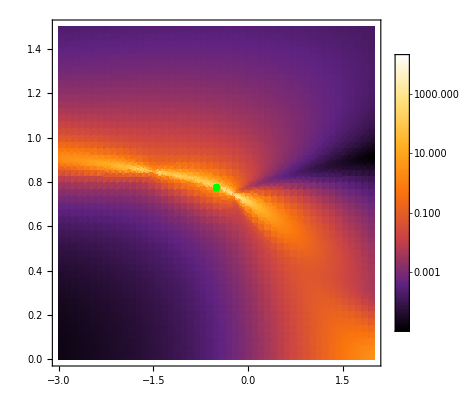

```mathematica
SpMinPlot=ListPlot[{λ,χ}/.Flatten[min,1][[#,2]]&/@Range[8],PlotStyle->Green];
Show[{det,SpMinPlot}]
```

```mathematica
singularities={3,{{λ->-1.5000132615810209,χ->0.845153128565168},{λ->-0.24999499149528312,χ->0.7453559336706176}}}
```

## Metric tensor

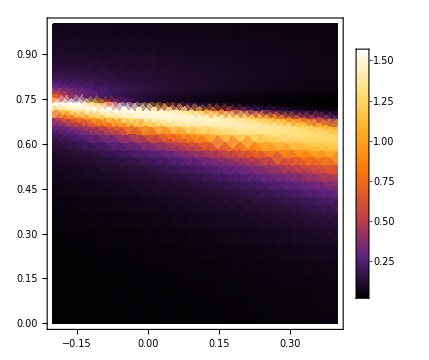
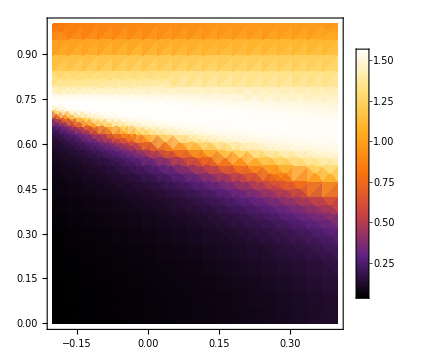
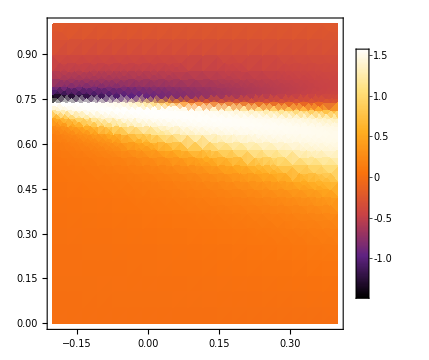

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
{DensityPlot[ArcTan[gC[y,x]⟦1,1⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦2,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦1,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen]}
```

#### Metric tensor determinant

```mathematica
DensityPlot[Det[gC[x,l]],{x,0,2.5},{l,0,2},Evaluate@densityPlotOptions,PlotPoints->300,ScalingFunctions->"Log10",PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[Det[gC[l,x]],{l,-0.5,2.5},{x,0,2},PlotPoints->50,Evaluate@font,ScalingFunctions->"Log10", ColorFunction->"SunsetColors",AxesLabel->MaTeX/@{"\\lambda","\\chi","Det(g)"}]
```

-Graphics3D-

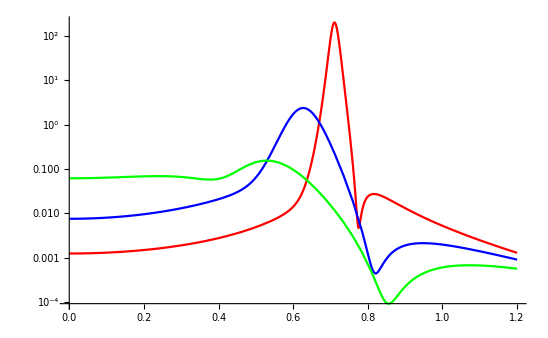

```mathematica
Plot[Evaluate[Det[gC[#,x]]&/@{0,0.5,1}],{x,0,1.2},PlotStyle->{Red,Blue,Green,Magenta,Purple},ScalingFunctions->"Log10"]
```

# Compiled geod function and Christoffel symbols

For huge matrices compute only first few energies and check for precission {vals,vecs}=Eigensystem[s,10]

Enable more functions to be compilable, for example Inverse

```mathematica
(*Internal`CompileValues[];(*to trigger auto-load*)ClearAttributes[Internal`CompileValues,ReadProtected];
syms=DownValues[Internal`CompileValues]/.HoldPattern[Verbatim[HoldPattern][Internal`CompileValues[sym_]]:>_]:>sym;
Complement[syms,Compile`CompilerFunctions[]]*)
```

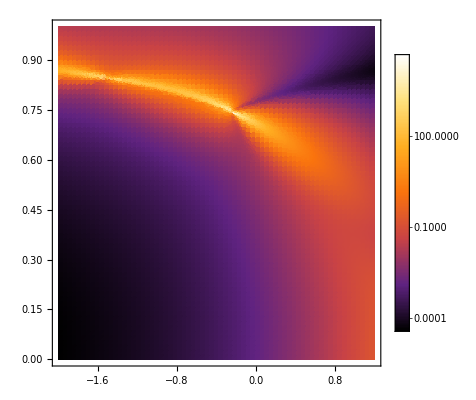

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->70]
```

## Define area for derivative precision

```mathematica
(*{{3,-1/2,√(3/5)},{4,-0.333,0.756},{5,-0.2501,0.7454},{6,-0.2,0.738},{7,-0.173,0.7346},{8,-0.14,0.73},{9,-0.1255,0.7277},{10,-0.1111,0.7255},{11,-0.1,0.7238},{12,-0.09,0.7223},{13,-0.0834,0.7211},{14,-0.0769,0.72}};*)
{c1,c2}={-0.1111,0.7255};
derPiece[λ_?NumericQ,χ_?NumericQ]:=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ-c1)^2+(Abs[χ]-c2)^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
Plot3D[derPiece[λ,χ],{λ,-6,6},{χ,-3,3},PlotLegends->Automatic,PlotPoints->30,PlotRange->All,ColorFunction->"SunsetColors"]
```

-Graphics3D-

## Christoffel symbols

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
(*G1[λ_?NumericQ,χ_?NumericQ]=Module[{derTerms,c,l,dg1,dg2,gInv1,gInv2},
derTerms=derPieceC[λ,χ];
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦1,#⟧&/@{1,2};
{gInv1 dg1⟦1,1⟧+gInv2(2dg1⟦1,2⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}
];
G2[λ_?NumericQ,χ_?NumericQ]=Module[{derTerms,c,l,dg1,dg2,gInv1,gInv2},
derTerms=derPieceC[λ,χ];
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦2,#⟧&/@{1,2};
{ gInv1 dg1⟦1,1⟧+ gInv2(dg1⟦1,2⟧+dg1⟦2,1⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}
]*)
(*Removing λ from derTerms executes normally, defining as := removes this problem, but then it cant select elements [[1,2]] WTFFFFFF??????
G1[λ_?NumericQ,χ_?NumericQ]=Module[{derTerms,c,l,dg1,dg2,gInv1,gInv2},
derTerms=5.5+λ;
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->Round@derTerms],ND[gC[λ,c],c,χ,Terms->Round@derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦1,#⟧&/@{1,2};
dg1⟦1,1⟧
(*{gInv1 dg1⟦1,1⟧+gInv2(2dg1⟦1,2⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}*)
];
ParallelTable[G1[1,i],{i,0,0.8,0.8}]*)
```

Check Christoffel symbols. If wrong, increase derTerms.

```mathematica
DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-0.2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->5]&/@{1,2,3}
DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-0.2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->5]&/@{1,2,3}
```

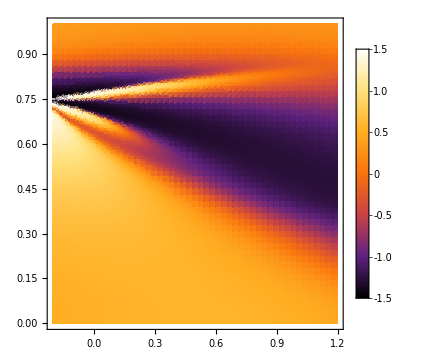
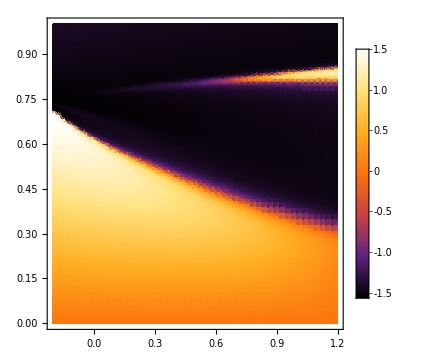
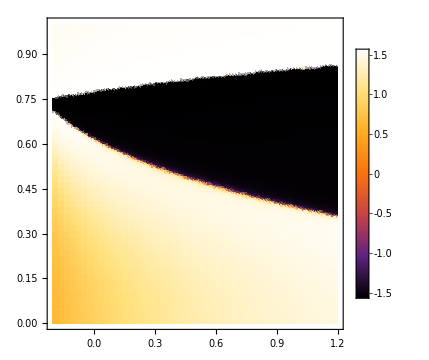

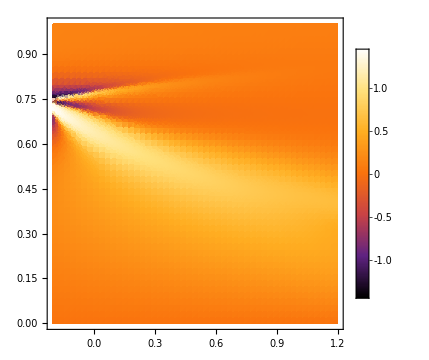
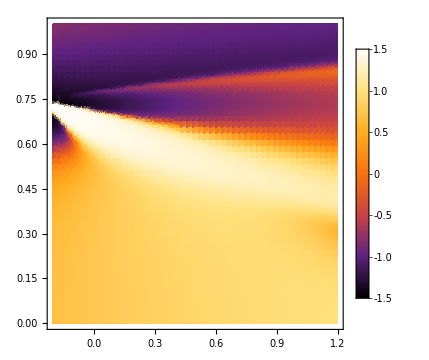
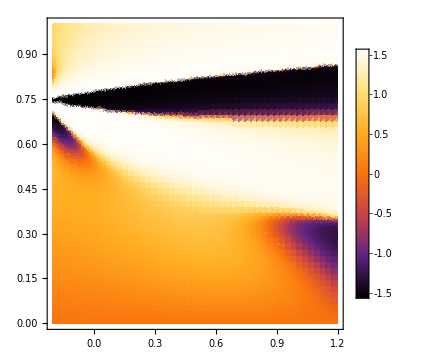

## Ricci and Riemann

```mathematica
RR[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,g1,g2},
derTerms=derPiece[λ,χ];
g1=G1[λ,χ];
g2=G2[λ,χ];
2/(gC[λ,χ]⟦1,1⟧)(ND[G2[λ,c],c,χ,Terms->derTerms]⟦1⟧-ND[G2[l,χ],l,λ,Terms->derTerms]⟦2⟧+g2⟦3⟧g2⟦1⟧+g2⟦2⟧g1⟦1⟧-g2⟦2⟧g2⟦2⟧-g2⟦1⟧g1⟦2⟧)
]
RR[-1/2,5]
```

-1.7288

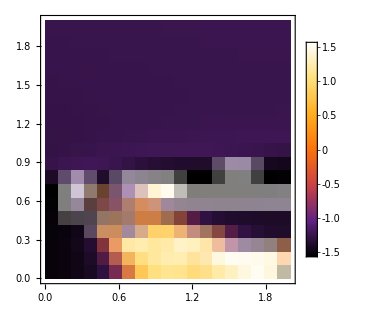

```mathematica
plRic=DensityPlot[ArcTan[RR[λ,χ]],{λ,-1,2},{χ,-1.5,1.5}, PerformanceGoal->"Quality",PlotPoints->50,ClippingStyle->Automatic,PlotLegends->Automatic,FrameLabel->{-Graphics-,-Graphics-},Evaluate@font,ColorFunction->"SunsetColors",ImageSize->310]
```

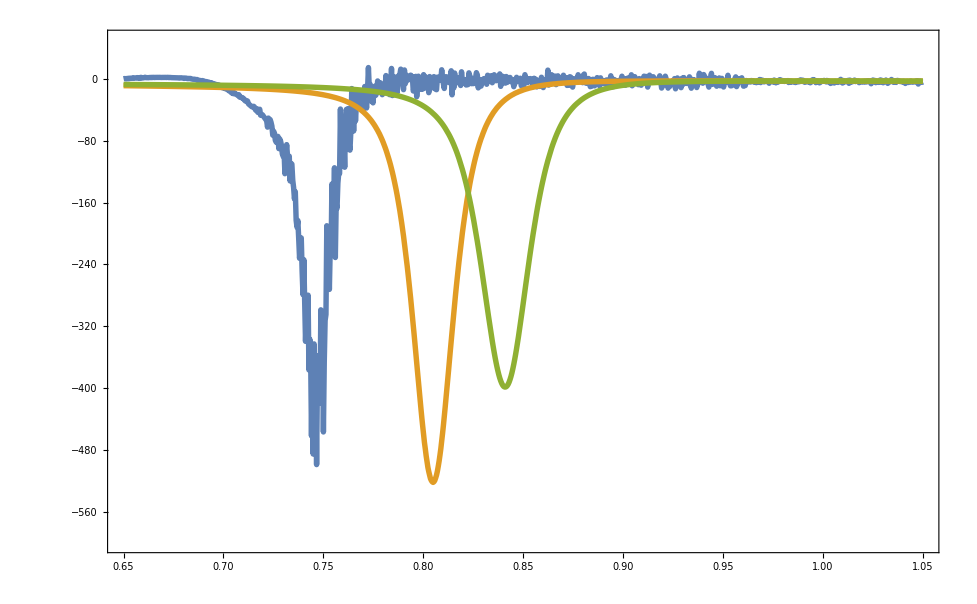

```mathematica
plRRS=Plot[{RR[0.2,χ],RR[1,χ],RR[1.5,χ]},{χ,0.65,1.05},Evaluate@plotOptions,FrameLabel->MaTeX/@{"\\chi","Ric"},PlotRange->{-600,50},PlotStyle->Thickness[0.004],PlotLegends->Placed[MaTeX/@{"\\lambda=0.2","\\lambda=1","\\lambda=1.5"},{0.8,0.2}],PlotPoints->15]
```

```mathematica
R1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=8;
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√Det[g])(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=8;
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√Det[g])(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
Ric[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,l,c,g},
derTerms=8;
g=gC[λ,χ];
1/(√Det[g])(ND[R1[l,χ],l,λ,Terms->derTerms]+ND[R2[λ,c],c,χ,Terms->derTerms])]
```

```mathematica
plRic=DensityPlot[ArcTan[Ric[λ,χ]],{λ,0,2},{χ,0,2}, PerformanceGoal->"Speed",PlotPoints->50,ClippingStyle->Automatic,PlotLegends->Automatic,FrameLabel->{-Graphics-,-Graphics-},Evaluate@font,ColorFunction->"SunsetColors",ImageSize->310]
```

## Boundary value problem

```mathematica
tmax=10;
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
Timing@NDSolve[Join[eq,dirichlet[0,0,0,0.2]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2,WorkingPrecision->100,Method->"ExplicitRungeKutta"]
```

NDSolve::precw: The precision of the differential equation ({{G1[λ[t],χ[t]].{((«1»)^(«1»)[«1»])^2,2 («1»)^(«1»)[«1»] («1»)^(«1»)[«1»],((«1»)^(«1»)[«1»])^2}+λ''[t]==0,G2[λ[t],χ[t]].{((«1»)^(«1»)[«1»])^2,2 («1»)^(«1»)[«1»] («1»)^(«1»)[«1»],((«1»)^(«1»)[«1»])^2}+χ''[t]==0,λ[0]==0,χ[0]==0,λ[10]==0,χ[10]==0.2},{},{},{},{}}) is less than WorkingPrecision (100.).

{37.117,{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
(*solP=ParametricNDSolve[Join[eq,dirichlet[0,0,0.3,f2]],{λ,χ},{t,0,tmax},{f2},PrecisionGoal->2,AccuracyGoal->2]
ParametricPlot[Evaluate@Table[{λ[f2][t],χ[f2][t]}/.solP,{f2,0,2,1}],{t,0,10},PlotRange->All]*)
```

```mathematica
Plot[Evaluate[x[t]/.sols],{t,0,10},PlotStyle->{Black,Blue,Green}]
```

```mathematica
solM=Quiet@ParallelTable[NDSolve[Join[eq,dirichlet[0,0,1,i]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.8,0.2}]
```

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM2,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

-Graphics-

```mathematica
RungeKutta
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

## Initial value problem

```mathematica
tmaxI=10;
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
sol=Quiet@NDSolve[Join[eq,cauchy[0,0,Cos[3],Sin[3]]],{λ,χ},{t,0,1000},PrecisionGoal->2,AccuracyGoal->2]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-30,1},{χ,0,10},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->10];
geodInitial=ParametricPlot[{λ[t],χ[t]}/.sol,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

-Graphics-

```mathematica
solMulti=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmaxI},AccuracyGoal->2,PrecisionGoal->2],{θ,0,π,π/50}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000291409,-15.3933},{-15.3933,5.5882×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000294612,-17.5377},{-17.5377,5.88768×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00774567,123.897},{123.897,2.07323×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00773447,124.713},{124.713,2.10303×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00441516,49.9128},{49.9128,580032.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0043997,49.9481},{49.9481,582882.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0117014,114.627},{114.627,1.14779×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0117014,114.627},{114.627,1.14779×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0116905,114.725},{114.725,1.1508×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.74799, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.80022, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.74561, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.76174, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.78384, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.78, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000118356,0.38816},{0.38816,20898.9}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000328838,8.7459},{8.7459,2.51485×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000624986,10.7555},{10.7555,198165.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000490358,8.87397},{8.87397,173440.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 8.48247, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.83087, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.8981, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.83055, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.03219×10^-10,-3.27325×10^-7},{-3.27325×10^-7,0.000177624}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{5.93822×10^-10,-3.23286×10^-7},{-3.23286×10^-7,0.000176009}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at Notebook$$91$216541`t == 7.72248; unable to continue.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.72051, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.63827, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 9.15412, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.96101, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.59792, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 8.0486, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 9.93558, step size is effectively zero; singularity or stiff system suspected.

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
geodInitial=ParametricPlot[{λ[t],χ[t]}/.solMulti,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

-Graphics-

# Direct minimalization

Find geodesics by minimizing the expression for fidelity.

# Singularity and stuff

```mathematica
nn=5;
jj=nn/2; 
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
maxPoints=Quiet@Table[FindMaximum[Det[gC[λ,χ]],{{λ,i},{χ,j}}],{i,-5,5,0.1},{j,0,2,0.1}];
```

```mathematica
maxPointsD=DeleteDuplicates@maxPoints;
Show[DensityPlot[Det@gC[λ,χ],{λ,-5,5},{χ,0,2},ScalingFunctions->"Log10"],Graphics[{Red,PointSize[Large],Point[{λ,χ}/.Map[Last,maxPointsD,2]]}]]
```

-Graphics-

```mathematica
Manipulate[DensityPlot[Det@gC[λ,χ],{λ,λmin,λmax},{χ,χmin,χmax},PlotPoints->PPoints,ScalingFunctions->"Log"],
{{λmin,-0.15},-2,0},{{λmax,0},-2,0},{{χmin,0.7},0,1},{{χmax,0.75},0,1},{{PPoints,30},5,100,1}]
```

### Energy difference singularity

```mathematica
enSing[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
Manipulate[DensityPlot[enSing[λ,χ]⟦1⟧-enSing[λ,χ]⟦2⟧,{λ,λmin,λmax},{χ,χmin,χmax},PlotPoints->20],
{{λmin,-0.5},-2,0},{{λmax,0},-2,0},{χmin,0,1},{{χmax,1},0,1},{{PPoints,15},5,100,1}]
```

# Playing with Hamiltonian form

```mathematica
Hp=Subscript[J, 3]-Λ/(2j)(1/4(SubPlus[J]+SubMinus[J])^2+Χ^2(Subscript[J, 3]^2+j^2+2j Subscript[J, 3])+Χ((SubPlus[J]+SubMinus[J]) Subscript[J, 3]+Subscript[J, 3](SubPlus[J]+SubMinus[J]))+2Χ j (SubPlus[J]+SubMinus[J]))
```

J_3-(Λ (2 j Χ (J_-+J_+)+1/4 (J_-+J_+)^2+2 Χ (J_-+J_+) J_3+Χ^2 (j^2+2 j J_3+J_3^2)))/(2 j)

```mathematica
OverHat[Subscript[p, x]]:=-I ℏ D[#, x] &;
OverHat[Subscript[p, y]]:=-I ℏ D[#, y] &;
OverHat[Subscript[p, z]]:=-I ℏ D[#, z] &;
```

```mathematica
Hd=I ℏ(x D[ψ[x,y,z],y]-y D[ψ[x,y,z],x])+λ V1d+χ V2d+χ^2 V3d;
V1d=ℏ^2/(2j)(y^2 D[ψ[x,y,z],{z,2}]-y D[ψ[x,y,z],y]-y z D[ψ[x,y,z],z,y]-z D[ψ[x,y,z],z]-z y D[ψ[x,y,z],y,z]+z^2 D[ψ[x,y,z],{y,2}]);
V2d=-1/(2j)(-2 ℏ^2(y x D[ψ[x,y,z],z,y]-y^2 D[ψ[x,y,z],x,z]-z x D[ψ[x,y,z],{y,2}]+z y D[ψ[x,y,z],y,x])-ℏ^2(z D[ψ[x,y,z],x]+x D[ψ[x,y,z],z]));
V3d=-1/(2j)(-ℏ^2(x^2 D[ψ[x,y,z],{y,2}]-x D[ψ[x,y,z],x]-x y D[ψ[x,y,z],x,y]-y D[ψ[x,y,z],y]-y x D[ψ[x,y,z],x,y]+y^2 D[ψ[x,y,z],{x,2}])+2j I ℏ(x D[ψ[x,y,z],y]-y D[ψ[x,y,z],x])+j^2 ψ[x,y,z]);
```

```mathematica
ℒ=Hd/.{ℏ->1,χ->2,λ->4,j->3};
ℬ=DirichletCondition[ψ[x,y,z]==0,True];
ℬd=DirichletCondition[Grad[ψ[x,y,z],{x,y,z}]==0,True];
```

```mathematica
DSolve[{Hd==e ψ[x,y,z],ℬ,ℬd},ψ,{x,y,z}]
```

```mathematica
NDEigenvalues[{ℒ,ℬ},ψ[x,y,z],{x,y,z}∈Ball[{0,0,0},10000000],2]//TraditionalForm
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{«1»},{«1»}},{2.61552×10^17+0. ⅈ,6.99333×10^15+0. ⅈ,7.03244×10^15+0. ⅈ,8.37866×10^15+0. ⅈ,1.10189×10^16+0. ⅈ,1.30547×10^16+0. ⅈ,8.81931×10^15+0. ⅈ,6.9154×10^15+0. ⅈ,«238801»,5.45526×10^16+0. ⅈ,5.45526×10^16+0. ⅈ,5.80982×10^15+0. ⅈ,4.08629×10^16+0. ⅈ,4.08629×10^16+0. ⅈ,1.46216×10^16+0. ⅈ,3.6929×10^16+0. ⅈ,1.32345×10^17+0. ⅈ}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{-1.50012,-1.50063}

### Up

```mathematica
Hup=Hd/.{x->0,y->0};
ℒup=Hup/.{ℏ->1,χ->2,λ->4,j->3}
```

-6 ψ[0,0,z]+2/3 (-z ψ^(0,0,1)[0,0,z]+z^2 ψ^(0,2,0)[0,0,z])+1/3 z ψ^(1,0,0)[0,0,z]

```mathematica
NDEigenvalues[{ℒup,ℬ},ψ[x,y,z],{x,y,z}∈Ball[{0,0,0},10],2]//TraditionalForm
```

NDEigenvalues::dvlen: The function ψ[0,0,z] does not have the same number of arguments as independent variables (4).

NDEigenvalues[{2/3 (z^2 ψ^(0,2,0)(0,0,z)-z ψ^(0,0,1)(0,0,z))+1/3 z ψ^(1,0,0)(0,0,z)-6 ψ(0,0,z),DirichletCondition[ψ(x,y,z)==0,True]},ψ(x,y,z),{x,y,z}∈Ball[{0,0,0},10],2]

```mathematica
upSol=DSolve[ℒup==e ψ[x,y,z],ψ,{x,y,z}]
```

{{ψ→Function[{x,y,z},(-18 ψ[0,0,z]-2 z ψ^(0,0,1)[0,0,z]+2 z^2 ψ^(0,2,0)[0,0,z]+z ψ^(1,0,0)[0,0,z])/(3 ⅇ)]}}

```mathematica
ψ[0,0,1]/.upSol
```

{(-18 ψ[0,0,1]-2 ψ^(0,0,1)[0,0,1]+2 ψ^(0,2,0)[0,0,1]+ψ^(1,0,0)[0,0,1])/(3 ⅇ)}

### χ = 0

```mathematica
Hup=Hd/.{χ->0};
ℒup=Hup/.{ℏ->1,λ->1,j->3,z->0}
```

1/6 (y^2 ψ^(0,0,2)[x,y,0]-y ψ^(0,1,0)[x,y,0])+ⅈ (x ψ^(0,1,0)[x,y,0]-y ψ^(1,0,0)[x,y,0])

```mathematica
NDEigenvalues[{ℒup,ℬ},ψ[x,y,z],{x,y,z}∈Ball[{0,0,0},10],2]//TraditionalForm
```

NDEigenvalues::derlen: The length of the derivative operator Derivative[0,0,2] in ψ^(0,0,2)[x,y,0] is not the same as the number of arguments.

NDEigenvalues[{1/6 (y^2 ψ^(0,0,2)(x,y,0)-y ψ^(0,1,0)(x,y,0))+ⅈ (x ψ^(0,1,0)(x,y,0)-y ψ^(1,0,0)(x,y,0)),DirichletCondition[ψ(x,y,z)==0,True]},ψ(x,y,z),{x,y,z}∈Ball[{0,0,0},10],2]

```mathematica
upSol=DSolve[ℒup==e ψ[x,y,z],ψ,{x,y,z}]
```

{{ψ→Function[{x,y,z},(y^2 ψ^(0,0,2)[x,y,0]-y ψ^(0,1,0)[x,y,0]+6 ⅈ (x ψ^(0,1,0)[x,y,0]-y ψ^(1,0,0)[x,y,0]))/(6 e)]}}